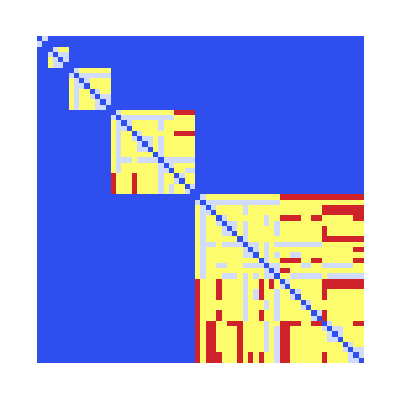
```mathematica
-Graphics-"{0,0,s___}->{0, 0, 1}
{1,0,s___}->{0, 0, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 0, 0}"
```

```mathematica
NestGraph[ReplaceList[{
{left___,0,0,s___}:>{left,s,0,0,1},
{left___,1,0,s___}:>{left,s,0,0,1},
{left___,0,1,s___}:>{left,s,0,0,1},
{left___,1,1,s___}:>{left,s,0,0,1}}],{{1,0,0}},5,VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),GraphLayout->"LayeredDigraphEmbedding",PerformanceGoal->"Quality"]
```

-Graphics-

```mathematica
{{"[◼]", "BranchialGraph"}}[NestGraph[ReplaceList[{
{left___,0,0,s___}:>{left,s,0,0,1},
{left___,1,0,s___}:>{left,s,0,0,1},
{left___,0,1,s___}:>{left,s,0,0,1},
{left___,1,1,s___}:>{left,s,0,0,1}}],{{1,0,0}},5,VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),GraphLayout->"LayeredDigraphEmbedding",PerformanceGoal->"Quality"]]
```

-Graphics-

```mathematica
NestGraph[ReplaceList[{
{left___,0,0,s___}:>{left,s,0,0,1},
{left___,1,0,s___}:>{left,s,0,0,1},
{left___,0,1,s___}:>{left,s,0,0,1},
{left___,1,1,s___}:>{left,s,0,0,1}}],{{1,0,0}},5,VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),GraphLayout->"LayeredDigraphEmbedding",PerformanceGoal->"Quality"]
```

-Graphics-

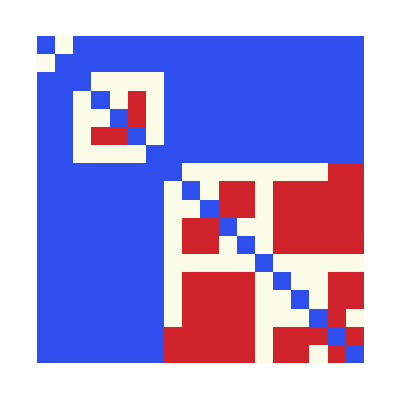
```mathematica
-Graphics-"{0,0,s___}->{0, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 1, 1}
{1,1,s___}->{0, 1, 1}
{1, 1, 1}"
```

```mathematica
NestGraph[ReplaceList[{
{left___,0,0,s___}:>{left,s,0,1,1},
{left___,1,0,s___}:>{left,s,0,1,1},
{left___,0,1,s___}:>{left,s,0,1,1},
{left___,1,1,s___}:>{left,s,0,1,1}}],{{1,1,1}},5,VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),GraphLayout->"LayeredDigraphEmbedding",PerformanceGoal->"Quality"]
```

-Graphics-

```mathematica
Table[
AllPathCanyons[
NestGraph[
ReplaceList[{
{left___,0,0,s___}:>{left,s,0,0,1},
{left___,1,0,s___}:>{left,s,0,1,1},
{left___,0,1,s___}:>{left,s,0,1,1},
{left___,1,1,s___}:>{left,s,0,1,1}
}],
{{0,1,0}},
10,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"
]],
{i,1,10}
]
```

$Aborted